```mathematica
data1 = Partition[Riffle[{0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25,6.75,7.25,7.75,8.25,8.75,9.25,9.75,10.25,10.75,11.25,11.75,12.25,12.75,13.25,13.75,14.25,14.75,15.25,15.75,16.25,16.75,17.25,17.75,18.25,18.75,19.25,19.75,20.25,20.75,21.25,21.75,22.25,22.75,23.25,23.75,24.25,24.75,25.25,25.75,26.25,26.75,27.25,27.75,28.25,28.75,29.25,29.75,30.25,30.75,31.25,31.75,32.25,32.75,33.25,33.75,34.25,34.75,35.25,35.75,36.25,36.75,37.25,37.75,38.25,38.75,39.25,39.75,40.25,40.75,41.25,41.75,42.25,42.75,43.25,43.75,44.25,44.75,45.25,45.75,46.25,46.75,47.25,47.75,48.25,48.75,49.25,49.75,50.25,50.75,51.25,51.75,52.25,52.75,53.25,53.75,54.25,54.75,55.25,55.75,56.25,56.75,57.25,57.75,58.25,58.75,59.25,59.75,60.25,60.75,61.25,61.75,62.25,62.75,63.25,63.75,64.25,64.75,65.25,65.75,66.25},{0.77337398,0.76545699,0.76976451,0.77566201,0.76424476,0.76974758,0.75651198,0.75528746,0.74744284,0.7425988,0.73916064,0.7291967,0.72403297,0.70979838,0.70251689,0.68867336,0.67639552,0.6629861,0.6520433,0.63337921,0.61562672,0.6020145,0.58242852,0.56392091,0.54517048,0.51694877,0.49012439,0.46644513,0.44328899,0.41533238,0.39627692,0.36685386,0.34132863,0.32021028,0.2976334,0.27532543,0.26048335,0.23729701,0.22180195,0.20523671,0.18997039,0.1750486,0.16192869,0.15195946,0.14159707,0.12990245,0.12240249,0.11668954,0.10656797,0.10077294,0.09039752,0.08754303,0.08169498,0.07821174,0.07387985,0.0704833,0.06503716,0.06204774,0.05943374,0.05561199,0.05531194,0.05190485,0.05141663,0.0482202,0.0467482,0.04698077,0.04358249,0.04273581,0.04247358,0.03932737,0.03952364,0.03785267,0.03633167,0.03385049,0.03458076,0.03284739,0.03484771,0.03164762,0.02983193,0.03116811,0.02858147,0.02992962,0.02745702,0.02745654,0.02740279,0.02686653,0.02449947,0.02459193,0.02504618,0.02353026,0.02373286,0.02417876,0.0235732,0.02235657,0.02161277,0.02039405,0.01985619,0.01949541,0.01906859,0.01886615,0.01897319,0.0190737,0.01745601,0.01898764,0.0189177,0.0166294,0.01590314,0.01578105,0.01575521,0.01638692,0.01515539,0.0141496,0.01499305,0.01602513,0.0148989,0.01570842,0.01533911,0.01491063,0.01446705,0.0163617,0.01482083,0.01531184,0.01427261,0.01698613,0.01486277,0.0164934,0.0159312,0.01496474,0.01636689,0.01621553,0.01669151,0.01432356,0.01664685}],2];
data2 = Partition[Riffle[{0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25,6.75,7.25,7.75,8.25,8.75,9.25,9.75,10.25,10.75,11.25,11.75,12.25,12.75,13.25,13.75,14.25,14.75,15.25,15.75,16.25,16.75,17.25,17.75,18.25,18.75,19.25,19.75,20.25,20.75,21.25,21.75,22.25,22.75,23.25,23.75,24.25,24.75,25.25,25.75,26.25,26.75,27.25,27.75,28.25,28.75,29.25,29.75,30.25,30.75,31.25,31.75,32.25,32.75,33.25,33.75,34.25,34.75,35.25,35.75,36.25,36.75,37.25,37.75,38.25,38.75,39.25,39.75,40.25,40.75,41.25,41.75,42.25,42.75,43.25,43.75,44.25,44.75,45.25,45.75,46.25,46.75,47.25,47.75,48.25,48.75,49.25,49.75,50.25,50.75,51.25,51.75,52.25,52.75,53.25,53.75,54.25,54.75,55.25,55.75,56.25,56.75,57.25,57.75,58.25,58.75,59.25,59.75,60.25,60.75,61.25,61.75,62.25,62.75},{0.78606477,0.80424984,0.79550342,0.80268476,0.78944487,0.79389935,0.78723241,0.78521198,0.78522255,0.77662802,0.7689769,0.76297234,0.75978247,0.74356309,0.7367435,0.72577028,0.70466669,0.69973457,0.67223122,0.6606004,0.64775839,0.62329956,0.60582956,0.59033638,0.56279306,0.54257372,0.51957432,0.48912465,0.46023969,0.44030073,0.4145497,0.38371018,0.35947505,0.33976821,0.31585908,0.2951042,0.2718557,0.25355123,0.23423784,0.21749137,0.203119,0.1830054,0.17308505,0.15976917,0.14709727,0.13877217,0.129329,0.12250633,0.11502097,0.10088223,0.09991389,0.09193491,0.08849412,0.08452146,0.07717952,0.07593273,0.07041274,0.06720639,0.0662632,0.06146676,0.05978082,0.05566419,0.05425513,0.05219703,0.05012368,0.04783904,0.04991266,0.04453292,0.04437397,0.04300747,0.04240035,0.04107839,0.04052386,0.03901737,0.0389992,0.03791944,0.03415949,0.03523265,0.03406836,0.03460269,0.0331519,0.03191466,0.03039971,0.02976486,0.03027112,0.02875204,0.02777904,0.02803252,0.0263271,0.02572687,0.02552032,0.02388113,0.02425255,0.02410074,0.02371515,0.02312375,0.02111159,0.02154955,0.0203748,0.02046483,0.02008392,0.01995903,0.01939966,0.02099564,0.01977694,0.01970291,0.02037383,0.01900328,0.01983651,0.01966778,0.02052543,0.01963565,0.01963804,0.01884302,0.01968109,0.02032015,0.02028343,0.01921917,0.01904885,0.01926113,0.02043689,0.02104981,0.02012339,0.01959632,0.0173213,0.01849315}],2];
data3 = Partition[Riffle[{0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25,6.75,7.25,7.75,8.25,8.75,9.25,9.75,10.25,10.75,11.25,11.75,12.25,12.75,13.25,13.75,14.25,14.75,15.25,15.75,16.25,16.75,17.25,17.75,18.25,18.75,19.25,19.75,20.25,20.75,21.25,21.75,22.25,22.75,23.25,23.75,24.25,24.75,25.25,25.75,26.25,26.75,27.25,27.75,28.25,28.75,29.25,29.75,30.25,30.75,31.25,31.75,32.25,32.75,33.25,33.75,34.25,34.75,35.25,35.75,36.25,36.75,37.25,37.75,38.25,38.75,39.25,39.75,40.25,40.75,41.25,41.75,42.25,42.75,43.25,43.75,44.25,44.75,45.25,45.75,46.25,46.75,47.25,47.75,48.25,48.75,49.25,49.75,50.25,50.75,51.25,51.75,52.25,52.75,53.25,53.75,54.25,54.75,55.25,55.75,56.25,56.75,57.25,57.75,58.25,58.75,59.25,59.75,60.25,60.75,61.25,61.75,62.25,62.75,63.25,63.75,64.25,64.75,65.25,65.75,66.25},{0.78947368,0.76558773,0.7784744,0.76644157,0.76323988,0.77411967,0.74805195,0.75386927,0.74448516,0.75034284,0.73734374,0.72923344,0.72414681,0.71203059,0.6992892,0.68746094,0.67727323,0.6649134,0.64813852,0.64301631,0.61762483,0.59763833,0.58498481,0.56261259,0.54211782,0.51542527,0.49876621,0.46698999,0.44235594,0.42269248,0.39857781,0.37053306,0.34379024,0.32426794,0.29983866,0.27693813,0.2611975,0.24266798,0.22818609,0.20906108,0.19149413,0.17642266,0.16366978,0.15214277,0.13763391,0.13291175,0.12136328,0.11706898,0.10963976,0.10125849,0.09430342,0.08671963,0.08217346,0.07728075,0.07384839,0.07176439,0.06663475,0.06311393,0.06003115,0.05702137,0.05502073,0.05320244,0.05141172,0.04783821,0.04634031,0.04465234,0.04402445,0.04134454,0.04162918,0.03941388,0.03873376,0.03680802,0.03632561,0.03396235,0.03381298,0.03360879,0.03250642,0.03160266,0.03071625,0.03057811,0.02842207,0.02867208,0.02933561,0.02710336,0.02676146,0.02538107,0.02621223,0.02606755,0.02569466,0.02447887,0.02267331,0.02406423,0.02282853,0.02124582,0.02128777,0.02157831,0.01998764,0.01936483,0.01821472,0.02009885,0.01874342,0.01792233,0.01744569,0.01702339,0.01688223,0.01758242,0.01710249,0.01650673,0.01513692,0.01630086,0.01734996,0.01438238,0.01550367,0.01488119,0.01472091,0.01645395,0.01514452,0.01515743,0.01541624,0.01459194,0.01466976,0.01623627,0.01522993,0.01431453,0.01498452,0.01674799,0.01535129,0.01674641,0.01536925,0.01514091,0.01750987,0.01570471,0.01752229}],2];
data4 = Partition[Riffle[{0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25,6.75,7.25,7.75,8.25,8.75,9.25,9.75,10.25,10.75,11.25,11.75,12.25,12.75,13.25,13.75,14.25,14.75,15.25,15.75,16.25,16.75,17.25,17.75,18.25,18.75,19.25,19.75,20.25,20.75,21.25,21.75,22.25,22.75,23.25,23.75,24.25,24.75,25.25,25.75,26.25,26.75,27.25,27.75,28.25,28.75,29.25,29.75,30.25,30.75,31.25,31.75,32.25,32.75,33.25,33.75,34.25,34.75,35.25,35.75,36.25,36.75,37.25,37.75,38.25,38.75,39.25,39.75,40.25,40.75,41.25,41.75,42.25,42.75,43.25,43.75,44.25,44.75,45.25,45.75,46.25,46.75,47.25,47.75,48.25,48.75,49.25,49.75,50.25,50.75,51.25,51.75,52.25,52.75,53.25,53.75,54.25,54.75,55.25,55.75,56.25,56.75,57.25,57.75,58.25,58.75,59.25,59.75,60.25,60.75,61.25,61.75,62.25,62.75,63.25,63.75,64.25,64.75,65.25,65.75,66.25},{0.78265525,0.77428571,0.76557377,0.77235539,0.7674689,0.76751103,0.75842878,0.75044723,0.74616644,0.74405785,0.7288042,0.72475667,0.72561479,0.71015114,0.7002224,0.68787706,0.67690438,0.66153683,0.65195692,0.63478969,0.62165268,0.59048741,0.57908429,0.55786939,0.53860942,0.51355092,0.49618221,0.4654626,0.44407028,0.41186469,0.39158963,0.3691792,0.34062181,0.32552053,0.29974598,0.27898975,0.2549815,0.23832617,0.22327345,0.21133886,0.18935676,0.17535784,0.16667175,0.15251185,0.13869536,0.13595569,0.11822111,0.11646487,0.10802916,0.10123752,0.09233665,0.08840113,0.08461846,0.07738624,0.07425441,0.07003826,0.06615619,0.06232797,0.0605097,0.05786887,0.05462944,0.05183536,0.05162105,0.04916067,0.04792954,0.04458255,0.04467732,0.04148078,0.04038549,0.03808704,0.03718288,0.03771013,0.03665942,0.03536941,0.03473144,0.03366049,0.03371278,0.03187697,0.03117169,0.03041701,0.02858954,0.02937096,0.02898413,0.02698619,0.0266448,0.02759861,0.02673489,0.02598491,0.02475283,0.02461994,0.02407253,0.02400883,0.0214437,0.0230305,0.02065184,0.02093424,0.02098844,0.01975895,0.01957609,0.01793785,0.0187737,0.01807158,0.0174892,0.01754553,0.01666269,0.01626794,0.01634177,0.0151441,0.01631006,0.01668415,0.01440704,0.01515152,0.01582594,0.01578451,0.01578804,0.01477595,0.01505755,0.01549152,0.01465372,0.01543635,0.01400673,0.01494209,0.01524357,0.01472957,0.01481603,0.01601196,0.01546464,0.01510989,0.01498737,0.01677411,0.01654846,0.01550688,0.01169036}],2];
data5 = Partition[Riffle[{0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25,6.75,7.25,7.75,8.25,8.75,9.25,9.75,10.25,10.75,11.25,11.75,12.25,12.75,13.25,13.75,14.25,14.75,15.25,15.75,16.25,16.75,17.25,17.75,18.25,18.75,19.25,19.75,20.25,20.75,21.25,21.75,22.25,22.75,23.25,23.75,24.25,24.75,25.25,25.75,26.25,26.75,27.25,27.75,28.25,28.75,29.25,29.75,30.25,30.75,31.25,31.75,32.25,32.75,33.25,33.75,34.25,34.75,35.25,35.75,36.25,36.75,37.25,37.75,38.25,38.75,39.25,39.75,40.25,40.75,41.25,41.75,42.25,42.75,43.25,43.75,44.25,44.75,45.25,45.75,46.25,46.75,47.25,47.75,48.25,48.75,49.25,49.75,50.25,50.75,51.25,51.75,52.25,52.75,53.25,53.75,54.25,54.75,55.25,55.75,56.25,56.75,57.25,57.75,58.25,58.75,59.25,59.75,60.25,60.75,61.25,61.75,62.25,62.75},{0.80638916,0.80669856,0.7998006,0.79536405,0.78942798,0.79009371,0.78035354,0.78100087,0.78279168,0.77741425,0.77321825,0.76218691,0.75850267,0.74999015,0.73465403,0.7233512,0.7083002,0.69881703,0.68034841,0.66134146,0.64541833,0.62706483,0.60843422,0.58873895,0.57315128,0.54293801,0.51407579,0.48751682,0.46763289,0.43570638,0.4102407,0.38865127,0.36402336,0.33740756,0.3105958,0.29460677,0.26981816,0.25069248,0.23583569,0.21506978,0.20440298,0.18709677,0.17181012,0.15931764,0.15231948,0.13889995,0.12751817,0.12107567,0.11271947,0.10490127,0.0985269,0.09241554,0.08999953,0.08228183,0.0784345,0.07292982,0.06842532,0.06557047,0.06527404,0.06286901,0.05996695,0.05877354,0.05417238,0.0536598,0.04983657,0.04905332,0.04922977,0.04649851,0.04586051,0.04463679,0.04277795,0.04204059,0.03899488,0.0387761,0.03630333,0.03769801,0.03529333,0.03582627,0.03321639,0.03330113,0.03254997,0.03311348,0.03368602,0.02948458,0.02887834,0.03052917,0.0271403,0.02713698,0.02679396,0.02574802,0.02510667,0.0242147,0.02266308,0.02249369,0.02352595,0.02282331,0.02182481,0.0207916,0.02245882,0.02019352,0.0210089,0.0209197,0.02049441,0.01989249,0.01962281,0.0186773,0.01967696,0.01917062,0.01942976,0.01900745,0.0195776,0.0189626,0.01806456,0.02061482,0.0184185,0.01946669,0.01914022,0.01975249,0.02098887,0.02249647,0.01936483,0.02095076,0.02063995,0.01920521,0.01649418,0.01749514}],2];
data6 = Partition[Riffle[{0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25,6.75,7.25,7.75,8.25,8.75,9.25,9.75,10.25,10.75,11.25,11.75,12.25,12.75,13.25,13.75,14.25,14.75,15.25,15.75,16.25,16.75,17.25,17.75,18.25,18.75,19.25,19.75,20.25,20.75,21.25,21.75,22.25,22.75,23.25,23.75,24.25,24.75,25.25,25.75,26.25,26.75,27.25,27.75,28.25,28.75,29.25,29.75,30.25,30.75,31.25,31.75,32.25,32.75,33.25,33.75,34.25,34.75,35.25,35.75,36.25,36.75,37.25,37.75,38.25,38.75,39.25,39.75,40.25,40.75,41.25,41.75,42.25,42.75,43.25,43.75,44.25,44.75,45.25,45.75,46.25,46.75,47.25,47.75,48.25,48.75,49.25,49.75,50.25,50.75,51.25,51.75,52.25,52.75,53.25,53.75,54.25,54.75,55.25,55.75,56.25,56.75,57.25,57.75,58.25,58.75,59.25,59.75,60.25,60.75,61.25,61.75,62.25,62.75,63.25,63.75,64.25,64.75,65.25,65.75,66.25},{0.79575329,0.79285955,0.78137903,0.77525103,0.76445944,0.76274643,0.76198239,0.7523753,0.7536442,0.74237728,0.73901969,0.72774662,0.71578479,0.71102778,0.69790317,0.69173019,0.67754852,0.65899828,0.64677217,0.6375,0.61545768,0.59341893,0.57669693,0.55950042,0.54348919,0.51944294,0.49172972,0.46043822,0.44019483,0.4184043,0.39144372,0.36994035,0.34433365,0.3247811,0.29755714,0.28137791,0.26295572,0.2382152,0.22142809,0.20818441,0.19083019,0.17659702,0.16781377,0.15215819,0.13562924,0.13109896,0.12225459,0.11388176,0.104468,0.0979406,0.09347351,0.08770419,0.08486542,0.08002843,0.0754974,0.0690367,0.06675129,0.06428339,0.05964327,0.05674957,0.05543538,0.05394409,0.05082178,0.04781978,0.04682086,0.04535769,0.04350374,0.04260652,0.04172782,0.03896396,0.03807828,0.03757395,0.03661114,0.03494066,0.03282567,0.03342068,0.03296906,0.03189589,0.03164778,0.03160191,0.02865571,0.02833645,0.02838119,0.02672919,0.02705584,0.02588481,0.02640311,0.02558518,0.02453605,0.02514106,0.0248653,0.02229707,0.02321974,0.02198794,0.02178317,0.0219511,0.02051679,0.01994464,0.01983699,0.0193999,0.01906008,0.01791711,0.01780773,0.0167817,0.0167623,0.01715511,0.01711191,0.01571203,0.01628119,0.01524624,0.01563726,0.01560796,0.015625,0.01458697,0.01512818,0.01471084,0.01483602,0.01403939,0.01591504,0.0143771,0.015014,0.0153441,0.01561757,0.01465721,0.01406406,0.01553271,0.01490993,0.01530768,0.01384701,0.01537099,0.01688417,0.01457899,0.01626525}],2];
data7 = Partition[Riffle[{0.25,0.75,1.25,1.75,2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75,6.25,6.75,7.25,7.75,8.25,8.75,9.25,9.75,10.25,10.75,11.25,11.75,12.25,12.75,13.25,13.75,14.25,14.75,15.25,15.75,16.25,16.75,17.25,17.75,18.25,18.75,19.25,19.75,20.25,20.75,21.25,21.75,22.25,22.75,23.25,23.75,24.25,24.75,25.25,25.75,26.25,26.75,27.25,27.75,28.25,28.75,29.25,29.75,30.25,30.75,31.25,31.75,32.25,32.75,33.25,33.75,34.25,34.75},{0.71540726,0.71874006,0.71078431,0.70428122,0.70539507,0.70964145,0.71031046,0.70044543,0.6906071,0.68697097,0.67709815,0.6755579,0.66523553,0.65367149,0.64155844,0.63492933,0.61365561,0.59923084,0.59342315,0.58031454,0.56403901,0.54524588,0.53158534,0.5108449,0.48573324,0.47243102,0.44780652,0.42179021,0.40064651,0.37778458,0.35866781,0.33243259,0.30846596,0.28979629,0.27281788,0.25470854,0.23240095,0.21853916,0.2037363,0.18900257,0.17604777,0.16640158,0.15226326,0.14270259,0.13398168,0.12772161,0.11860904,0.11081922,0.10365156,0.10030515,0.0920606,0.08986024,0.08446663,0.08247156,0.07731455,0.07421249,0.07282748,0.06860518,0.06763679,0.06524483,0.06495443,0.06533985,0.06293536,0.06423508,0.06370048,0.06317089,0.06440123,0.06597184,0.06869755,0.07292012}],2];
```

```mathematica
model1 = A/(1+g^2*r^2)^(3/2)+m*r+b;
model1parameters = {A,g,m,b};
model2 = A*Exp[-a*(r/r0)/(1+(r/r0)^(1-alpha))-b/(1+(r/r0)^(-alpha))];
model2parameters = {A,r0,a,b,alpha};
model3 = V0/(1+Exp[(r-R)/a])+d;
model3parameters = {V0,R,a,d};

model4 = V0/(1+Exp[(r-R)/a])+d + m * r;
model4parameters = {V0,R,a,d, m};
```

{V0→0.726032,R→14.3708,a→3.98461,d→0.0123895,m→0.00139781}

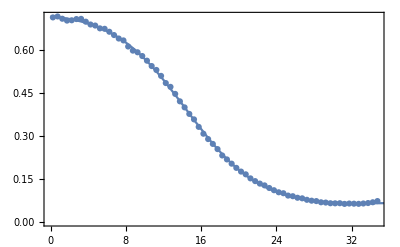

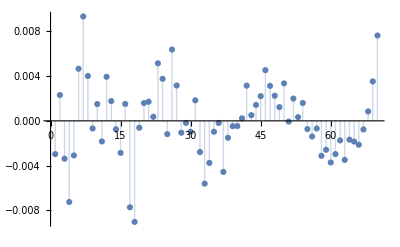

```mathematica
data = data7;
model = model4;
modelparameters = model4parameters;
(*data = Take[data, 60];*)
nlm=NonlinearModelFit[data,model,modelparameters,r];
nlm["BestFitParameters"]
(*Print[A/.nlm["BestFitParameters"]]
Print[r0/.nlm["BestFitParameters"]]
Print[a/.nlm["BestFitParameters"]]
Print[b/.nlm["BestFitParameters"]]
Print[alpha/.nlm["BestFitParameters"]]*)
(*nlm["ParameterTable"]*)
Show[ListPlot[data, Frame->True],Plot[Normal[nlm],{r,0,75}]]
ListPlot[nlm["FitResiduals"],Filling->Axis]
```